```mathematica
Nt = 455;
ti = 0; tf = 14; (*5*)
deltat = (tf - ti) /Nt ;
Nx =455; (*455*)
(*xi = -2; xf = 8;*)
xi = -20; xf = 20; (*-40 to 40*)
deltax = (xf - xi) / Nx;
c =  1;
r = c * (deltat / deltax)//N
```

0.35

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
```

```mathematica
T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1}],32];

(*For Perodic Interpolation*) 
Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

X= N[Table[xm = xi + m *deltax, {m, 0, Nx - 1}],32];

f[x_] =ⅇ^(- (x)^2);

fexact[t_,x_] = ⅇ^(- ((x-t))^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrices*)
(************************************************************************************************************************)
```

```mathematica
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal), {i,1,2}],32];
DL2 = N[Table[(-c)^i * L2[[i]] * (deltat)^i,{i,1,2}],32];

L4 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal), {i,1,4}],32];
DL4 = N[Table[(-c)^i * L4[[i]] * (deltat)^i,{i,1,4}],32];

L6 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->6, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal), {i,1,6}],32];
DL6 = N[Table[(-c)^i * L6[[i]] * (deltat)^i,{i,1,6}],32];

L8 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->8, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL8 = N[Table[(-c)^i * L8[[i]] * (deltat)^i,{i,1,8}],32];
```

```mathematica
(*LD2*)
ULD2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD2[[1,All]] = N[f[X],32];
ULD2 = Chop[ULD2, 10^(-307)];
ULD2 = Developer`ToPackedArray[ULD2, Real]; 
Developer`PackedArrayQ[ULD2]


ILD2 = N[IdentityMatrix[Length[DL2[[1]]]],32];
ALD2 = N[ILD2 - ((DL2[[1]] / 2)),32];
BLD2 = N[ILD2 + ((DL2[[1]] / 2)),32];
MLD2 = N[Inverse[ALD2].BLD2,32];
EMLD2 = N[MLD2 - ILD2,32];
EMLD2 = Developer`ToPackedArray[EMLD2, Real]; 

Do[ULD2[[n+1,All]] = ULD2[[n,All]] + (EMLD2).ULD2[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = Chop[URK2, 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]

IRK2 = N[IdentityMatrix[Length[DL2[[1]]]],32];

MRK2 = N[(IRK2 + (DL2[[1]]) + ((1/2)*(DL2[[2]]))),32];

EMRK2 = N[MRK2 - IRK2,32];

EMRK2 = Developer`ToPackedArray[EMRK2, Real]; 

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD4*)
ULD4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD4[[1,All]] = N[f[X],32];
ULD4 = Chop[ULD4, 10^(-307)];
ULD4 = Developer`ToPackedArray[ULD4, Real]; 
Developer`PackedArrayQ[ULD4]

ILD4 = N[IdentityMatrix[Length[DL4[[1]]]],32];
ALD4 = N[ILD4 - ((DL4[[1]] / 2)) + (((DL4[[2]])/12)),32];
BLD4 = N[ILD4 + ((DL4[[1]] / 2)) + (((DL4[[2]])/12)),32];
MLD4 = N[Inverse[ALD4].BLD4,32];
EMLD4 = N[MLD4 - ILD4,32];

EMLD4 = Developer`ToPackedArray[EMLD4, Real]; 

Do[ULD4[[n+1,All]] = ULD4[[n,All]] + (EMLD4).ULD4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = Chop[URK4, 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]

IRK4 = N[IdentityMatrix[Length[DL4[[1]]]],32];

MRK4 = N[IRK4 + DL4[[1]] + ((1/2) * (DL4[[2]])) + ((1/6) * (DL4[[3]])) + ((1/24) * (DL4[[4]])),32];

EMRK4 = N[MRK4 - IRK4,32];

EMRK4 = Developer`ToPackedArray[EMRK4, Real]; 

Do[URK4[[n+1,All]] = URK4[[n,All]] + (EMRK4).URK4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD6*)
ULD6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD6[[1,All]] = N[f[X],32];
ULD6 = Chop[ULD6, 10^(-307)];
ULD6 = Developer`ToPackedArray[ULD6, Real]; 
Developer`PackedArrayQ[ULD6]


ILD6 = N[IdentityMatrix[Length[DL6[[1]]]],32];
ALD6 = N[ILD6 - ((DL6[[1]] / 2)) + ((DL6[[2]]/10)) - ((DL6[[3]]/120)),32];
BLD6 = N[ILD6 + ((DL6[[1]] / 2)) + ((DL6[[2]]/10)) + ((DL6[[3]]/120)),32];
MLD6 = N[Inverse[ALD6].BLD6,32];
EMLD6 = N[MLD6 - ILD6,32];

EMLD6= Developer`ToPackedArray[EMLD6, Real]; 

Do[ULD6[[n+1,All]] = ULD6[[n,All]] + (EMLD6).ULD6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK6*)
URK6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK6[[1,All]] = N[f[X],32];
URK6 = Chop[URK6, 10^(-307)];
URK6 = Developer`ToPackedArray[URK6, Real]; 
Developer`PackedArrayQ[URK6]

IRK6 = N[IdentityMatrix[Length[DL6[[1]]]],32];


MRK6 = N[IRK6 + DL6[[1]] + ((1/2) * DL6[[2]]) + ((1/6) * DL6[[3]]) + ((1/24) * DL6[[4]]) + ((1/120) * DL6[[5]]) + ((1/720) * DL6[[6]]),32];

EMRK6 = N[MRK6 - IRK6,32];

EMRK6= Developer`ToPackedArray[EMRK6, Real]; 

Do[URK6[[n+1,All]] = URK6[[n,All]] + (EMRK6).URK6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD8*)
ULD8= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD8[[1,All]] = N[f[X],32];
ULD8 = Chop[ULD8, 10^(-307)];
ULD8 = Developer`ToPackedArray[ULD8, Real]; 
Developer`PackedArrayQ[ULD8]


ILD8 = N[IdentityMatrix[Length[DL8[[1]]]],32];
ALD8 = N[ILD8 - ((DL8[[1]] / 2)) + (((3*DL8[[2]])/28)) - ((DL8[[3]]/84)) + ((DL8[[4]]/1680)),32];
BLD8 = N[ILD8 + ((DL8[[1]] / 2)) + (((3*DL8[[2]])/28)) + (((DL8[[3]])/84)) + (((DL8[[4]])/1680)),32];
MLD8 = N[Inverse[ALD8].BLD8,32];
EMLD8 = N[MLD8 - ILD8,32];

EMLD8= Developer`ToPackedArray[EMLD8, Real]; 

Do[ULD8[[n+1,All]] = ULD8[[n,All]] + (EMLD8).ULD8[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*Partial Inversion Order 2*)
UP= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UP[[1,All]] = N[f[X],32];
UP = Chop[UP, 10^(-307)];
UP = Developer`ToPackedArray[UP, Real]; 
Developer`PackedArrayQ[UP]

selectwidth = 8;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(*Grid if you use the PeriodicInterpolation command when creating the L Matrix*)
(*grid=x0+(Range[totalpoints + 1]-middlepoint)Δx;*)

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[1],grid,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/Δx*)
(*This is done so the M Matrix can be created symbollically and be created for any CFL Number by putting in a value for r*)
r=.;
LPX = LP*((-1)^1)*((r*Δx)^1);


(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
(*Can use PeriodicInterpolation on the L Matrix if you add a +1 when defining the grid*)
gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX = LPX//.{r -> (deltat / deltax)};

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-LPX/2 ].(IP+LPX/2));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}];

(*(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx},{j,0,Nx}];*)

Ip = IdentityMatrix[Length[MP]];

EMP = MP - Ip;

EMP= Developer`ToPackedArray[EMP, Real]; 

Do[UP[[n+1,All]] = UP[[n,All]] + (EMP).UP[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*Partial Inversion Order 4*)
UP4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UP4[[1,All]] = N[f[X],32];
UP4 = Chop[UP4, 10^(-307)];
UP4 = Developer`ToPackedArray[UP4, Real]; 
Developer`PackedArrayQ[UP4]

selectwidth = 8;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(*Grid if you use the PeriodicInterpolation command when creating the L Matrix*)
(*grid=x0+(Range[totalpoints + 1]-middlepoint)Δx;*)

LP4 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],grid, "DifferenceOrder"->4]@"DifferentiationMatrix"//Normal), {i,1,2}],32];
DLP4 = N[Table[(-c)^i * LP4[[i]] * (deltat)^i,{i,1,2}],32];
DLP4[[1]] = DLP4[[1]]//. {Δx -> deltax};
DLP4[[2]] = DLP4[[2]]//. {Δx -> deltax};


(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
(*Can use PeriodicInterpolation on the L Matrix if you add a +1 when defining the grid*)
gn = Table[(DLP4[[i]][[middlepoint,All]]//Normal),{i,1,Length[DLP4]}]//Simplify//FullSimplify;
DLP4 = Table[Table[RotateRight[gn[[j]],i],{i,-selectwidth,selectwidth}],{j,1,Length[DLP4]}];

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[DLP4[[1]]]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
AP4 = N[IP - ((DLP4[[1]] / 2)) + (((DLP4[[2]])/12)),32];
BP4 = N[IP + ((DLP4[[1]] / 2)) + (((DLP4[[2]])/12)),32];
Mn4 = N[Inverse[AP4].BP4,32];

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn4[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP4 = Table[0,{i,1,Nx},{j,1,Nx}];



(*WITH Periodic Boundary Conditions*)
MP4 = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}];

(*(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx},{j,0,Nx}];*)

Ip4 = IdentityMatrix[Length[MP4]];

EMP4 = MP4 - Ip4;

EMP4= Developer`ToPackedArray[EMP4, Real]; 

Do[UP4[[n+1,All]] = UP4[[n,All]] + (EMP4).UP4[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*Don't need the Differentiation Matrices to have 32 digits anymore*)
{{L1 = Developer`ToPackedArray[L1, Real]; 
L2 = Developer`ToPackedArray[L2, Real];  
L4 = Developer`ToPackedArray[L4, Real]; 
L6 = Developer`ToPackedArray[L6, Real];
L8 = Developer`ToPackedArray[L8, Real];}, {}}
```

{{Null^5},{Null}}

```mathematica
(************************************************************************************************************************)
(* Eigenvalues*)
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
(*evalsLD2 = Eigenvalues[N[MLD2]];
realEvalsLD2 = Re[evalsLD2];
imagEvalsLD2 = Im[evalsLD2];
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK2*)
(*evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*LD4*)
(*evalsLD4 = Eigenvalues[N[MN]];
realEvalsN= Re[evalsN];
imagEvalsN = Im[evalsN];
ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)

(*RK4*)
(*evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
FLD2 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD2 = Developer`ToPackedArray[FLD2, Real];
intLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
intLD2 = Developer`ToPackedArray[intLD2, Real];
Do[
FLD2[[i,All]] = (L2[[1]].ULD2[[i,All]])^2;

intLD2[[i]] = (xf - xi)/Nx Total[FLD2[[i,All]]]
,{i,1,Length[FLD2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intCN}]},Joined->True]*)
```

```mathematica
(*RK2*)
FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
FRK2 = Developer`ToPackedArray[FRK2, Real];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = Developer`ToPackedArray[intRK2, Real];
Do[
FRK2[[i]] = (L2[[1]].URK2[[i,All]])^2;

intRK2[[i]] = (xf-xi)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},Joined->True]*)
```

```mathematica
(*LD4*)
FLD4 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD4 = Developer`ToPackedArray[FLD4, Real];
intLD4 = Table[0,{i,1,Length[FLD4[[All,1]]]}];
intLD4 = Developer`ToPackedArray[intLD4, Real];
Do[
FLD4[[i]] = (L4[[1]].ULD4[[i,All]])^2;

intLD4[[i]] = (xf-xi)/Nx Total[FLD4[[i,All]]]
,{i,1,Length[FLD4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intLD4}]},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
FRK4 = Developer`ToPackedArray[FRK4, Real];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
intRK4 = Developer`ToPackedArray[intRK4, Real];
Do[
FRK4[[i]] = (L4[[1]].URK4[[i,All]])^2;

intRK4[[i]] = (xf-xi)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK4}]},Joined->True]*)
```

```mathematica
(*LD6*)
FLD6 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD6 = Developer`ToPackedArray[FLD6, Real];
intLD6 = Table[0,{i,1,Length[FLD6[[All,1]]]}];
intLD6 = Developer`ToPackedArray[intLD6, Real];
Do[
FLD6[[i]] = (L6[[1]].ULD6[[i,All]])^2;

intLD6[[i]] = (xf-xi)/Nx Total[FLD6[[i,All]]]
,{i,1,Length[FLD6[[All,1]]]}];
```

```mathematica
(*RK6*)
FRK6 = Table[0,{i,1,Nt},{j,1,Nx}];
FRK6 = Developer`ToPackedArray[FRK6, Real];
intRK6 = Table[0,{i,1,Length[FRK6[[All,1]]]}];
intRK6 = Developer`ToPackedArray[intRK6, Real];
Do[
FRK6[[i]] = (L6[[1]].URK6[[i,All]])^2;

intRK6[[i]] = (xf-xi)/Nx Total[FRK6[[i,All]]]
,{i,1,Length[FRK6[[All,1]]]}];
```

```mathematica
(*LD8*)
FLD8 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD8 = Developer`ToPackedArray[FLD8, Real];
intLD8 = Table[0,{i,1,Length[FLD8[[All,1]]]}];
intLD8 = Developer`ToPackedArray[intLD8, Real];
Do[
FLD8[[i]] = (L8[[1]].ULD6[[i,All]])^2;

intLD8[[i]] = (xf-xi)/Nx Total[FLD8[[i,All]]]
,{i,1,Length[FLD8[[All,1]]]}];
```

```mathematica
(*Partial Inversion Order 2*)
FP = Table[0,{i,1,Nt},{j,1,Nx}];
FP = Developer`ToPackedArray[FP, Real];
intP = Table[0,{i,1,Length[FP[[All,1]]]}];
intP = Developer`ToPackedArray[intP, Real];
Do[
FP[[i]] = (L2[[1]].UP[[i,All]])^2;

intP[[i]] = (xf-xi)/Nx Total[FP[[i,All]]]
,{i,1,Length[FP[[All,1]]]}];
```

```mathematica
(*Partial Inversion Order 4*)
FP4 = Table[0,{i,1,Nt},{j,1,Nx}];
FP4 = Developer`ToPackedArray[FP4, Real];
intP4 = Table[0,{i,1,Length[FP4[[All,1]]]}];
intP4 = Developer`ToPackedArray[intP4, Real];
Do[
FP4[[i]] = (L4[[1]].UP4[[i,All]])^2;

intP4[[i]] = (xf-xi)/Nx Total[FP4[[i,All]]]
,{i,1,Length[FP4[[All,1]]]}];
```

```mathematica
energyErrorLD2 = Abs[intLD2 - intLD2[[1]]];
energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];
energyErrorLD4 = Abs[intLD4 - intLD4[[1]]];
energyErrorRK4 = Abs[intRK4 - intRK4[[1]]];
energyErrorLD6 = Abs[intLD6 - intLD6[[1]]];
energyErrorRK6 = Abs[intRK6 - intRK6[[1]]];
energyErrorLD8 = Abs[intLD8 - intLD8[[1]]];
energyErrorP = Abs[intP - intP[[1]]];
energyErrorPI4 = Abs[intP4 - intP4[[1]]];
```

```mathematica
(*ListLinePlot[{Transpose[{T,energyErrorLD2}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorLD4}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorRK2}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorRK4}]},Joined->True,PlotRange->All]*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

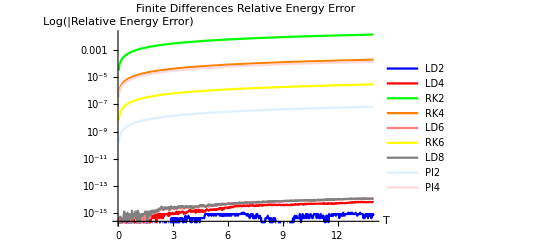

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}],Transpose[{T,energyErrorLD6}],Transpose[{T,energyErrorRK6}],Transpose[{T,energyErrorLD8}], Transpose[{T,energyErrorP}], Transpose[{T,energyErrorPI4}]},PlotStyle->{Blue, Red,Green, Orange,Pink,Yellow,Gray, LightBlue, LightRed},PlotLegends->{"LD2","LD4","RK2","RK4","LD6","RK6","LD8", "PI2", "PI4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Finite Differences Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4, energyErrorLD6,energyErrorRK6,energyErrorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FD_Energy_Error_Final_Test_50.dat",exportData,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*L1 Error*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
abserrLD2 = Abs[ULD2-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}]]*)
```

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
errorRK2 = Developer`ToPackedArray[errorRK2, Real];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

```mathematica
(*LD4*)
abserrLD4 = Abs[ULD4-Uexact];
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
errorLD4 = Developer`ToPackedArray[errorLD4, Real];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
errorRK4 = Developer`ToPackedArray[errorRK4, Real];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}]]*)
```

```mathematica
(*LD6*)
abserrLD6 = Abs[ULD6-Uexact];
errorLD6 = Table[0,{i,1,Length[abserrLD6]}];
errorLD6 = Developer`ToPackedArray[errorLD6, Real];
Do[
errorLD6[[i]] = Norm[abserrLD6[[i,All]], 1] * deltax;
,{i,1,Length[errorLD6]}
];
```

```mathematica
(*RK6*)
abserrRK6 = Abs[URK6-Uexact];
errorRK6 = Table[0,{i,1,Length[abserrRK6]}];
errorRK6 = Developer`ToPackedArray[errorRK6, Real];
Do[
errorRK6[[i]] = Norm[abserrRK6[[i,All]], 1] * deltax;
,{i,1,Length[errorRK6]}
];
```

```mathematica
(*LD8*)
abserrLD8 = Abs[ULD8-Uexact];
errorLD8 = Table[0,{i,1,Length[abserrLD8]}];
errorLD8 = Developer`ToPackedArray[errorLD8, Real];
Do[
errorLD8[[i]] = Norm[abserrLD8[[i,All]], 1] * deltax;
,{i,1,Length[errorLD8]}
];
```

```mathematica
(*Partial Inversion Order 2*)
abserrP = Abs[UP-Uexact];
errorP = Table[0,{i,1,Length[abserrP]}];
errorP = Developer`ToPackedArray[errorP, Real];
Do[
errorP[[i]] = Norm[abserrP[[i,All]], 1] * deltax;
,{i,1,Length[errorP]}
];
```

```mathematica
(*Partial Inversion Order 4*)
abserrPI4 = Abs[UP4-Uexact];
errorPI4 = Table[0,{i,1,Length[abserrPI4]}];
errorPI4 = Developer`ToPackedArray[errorPI4, Real];
Do[
errorPI4[[i]] = Norm[abserrPI4[[i,All]], 1] * deltax;
,{i,1,Length[errorPI4]}
];
```

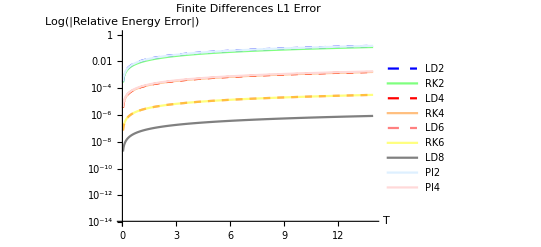

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}], Transpose[{T,errorLD6}], Transpose[{T,errorRK6}], Transpose[{T,errorLD8}], Transpose[{T,errorP}], Transpose[{T,errorPI4}]},PlotRange->{{ti,tf},{10^(-14),10^(0)}}, PlotStyle->{{Blue,Dashed},{Green,Opacity[0.5]},{Red,Dashed},{Orange,Opacity[0.5]},{Pink,Dashed},{Yellow,Opacity[0.5]},Gray,LightBlue, LightRed},PlotLabel->"Finite Differences L1 Error",PlotLegends->{"LD2","RK2","LD4","RK4","LD6","RK6","LD8","PI2", "PI4"},AxesLabel->{"T","Log(|Relative Energy Error|)"},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4,errorLD6,errorRK6,errorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FD_Error_Final_Test_50.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,UP[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{xi,xf},{0,1}}], {n,1,Nt ,1} ,AnimationRunning->False]
```

```mathematica
(*Animate[ListLinePlot[Transpose[{X,Abs[UCN[[n]] - Uexact[[n]]]}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]*)
```